```mathematica
data=Table[n=2^k;
{n,Mean[Table[Mean[Table[1/(1+RandomReal[]),{n}]],{1000}]]},{k,5,10}];
TableForm[data]
ListPlot[data,Joined->True]

errdata=Table[n=2^k;
{n,Mean[Table[Abs[Mean[Table[1/(1+RandomReal[]),{n}]-Log[2]]],{1000}]]},{k,5,10}];
TableForm[errdata]
f[x_]=j x^m;
fit=FindFit[errdata,f[x],{j,m},{x}]
f[x]/.fit;
Show[Plot[f[x]/.fit,{x,0,1200}],ListPlot[errdata,Joined->True]]
```

32 | 0.692084
64 | 0.693029
128 | 0.692884
256 | 0.692833
512 | 0.693051
1024 | 0.693163

-Graphics-

32 | 0.0202476
64 | 0.0137744
128 | 0.00983114
256 | 0.00686818
512 | 0.00478777
1024 | 0.00342778

{j→0.121754,m→-0.519465}

-Graphics-

```mathematica
data1=Table[p=1.30;
{x,Sech[p x]},{x,0.0,10,0.1}];
f1[x_]=Exp[-q x^2];
fit1=FindFit[data1,f1[x],{q},{x}]
f1[x]/.fit1;
Show[Plot[f1[x]/.fit1,{x,0,5},PlotStyle->{Red}],ListPlot[data1]]
```

{q→0.585786}

-Graphics-

```mathematica
Integrate[1/(1+x)^2,{x,0,1}]
Integrate[1/(1+x)^0.5,{x,0,1}]
Integrate[1/(1+x),{x,0,1}]
Integrate[1/(1+x)^3,{x,0,1}]
```

1/2

0.828427

Log[2]

3/8

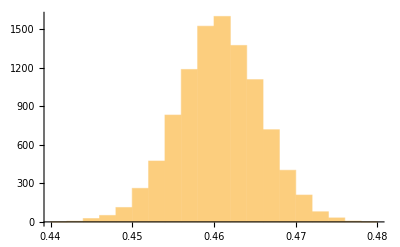

NormalDistribution[0.460655,0.00505018]

```mathematica
errdata1=Table[Mean[1/(1+RandomReal[{0,1},1000]^3)]-3/8,{10000}];
Histogram[errdata1]
FindDistribution[errdata1]
```

{47.627,{3.13852,3.14147,3.14175,3.14356,3.1409,3.14252,3.14253,3.1405,3.14145,3.1411,3.14232,3.14143,3.14296,3.14127,3.14295,3.14283,3.13958,3.14333,3.143,3.14387,3.14199,3.142,3.14343,3.13957,3.14049,3.14034,3.14035,3.1401,3.14167,3.13914,3.14056,3.14179,3.13876,3.14111,3.13879,3.14276,3.14198,3.14019,3.14174,3.14227,3.14194,3.14204,3.14099,3.14287,3.143,3.14411,3.14016,3.13969,3.13898,3.13781,3.14324,3.14069,3.14108,3.14142,3.1415,3.13936,3.14276,3.14168,3.14012,3.14014,3.14189,3.14333,3.13929,3.14348,3.14262,3.14128,3.14138,3.14057,3.14073,3.1437,3.14001,3.1388,3.1396,3.1425,3.1434,3.14237,3.14156,3.14235,3.13858,3.14249,3.14252,3.14022,3.14212,3.14315,3.14151,3.14109,3.14374,3.14487,3.14084,3.14249,3.14166,3.14061,3.14012,3.14614,3.14007,3.14166,3.14254,3.14248,3.14326,3.14203}}

3.14153

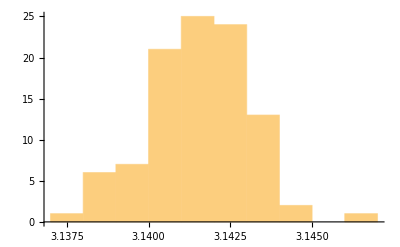

```mathematica
(dataset=Table[nMax=1000000;
4.0 (Table[If[(RandomReal[{0,1},2]^2//Total)≤1,1,0],nMax]//Total)/nMax,{100}])//Timing (*Finding a fraction of nMax no. of pins falling inside the unit circular-quadrant area as compared to the total square area enclosing the quadrant. Then multiplying the fraction by 4 to find the fraction of the pins in the entire circular area. Repeat the experiment 100 times*)
Mean[dataset]
Histogram[dataset]
```